# Lab 2 William Keilsohn Section 32 2/27/2014

1) Graphically determine the largest and smallest values of the given function on the interval [5,9] and also determine where local maximum and minimum are obtained.

```mathematica
Quit[]
```

```mathematica
f[x_]=6Cos[2x]+(5*x*Sin[x])/(x+1)
```

6 Cos[2 x]+(5 x Sin[x])/(1+x)

```mathematica
6 Cos[2 x]+(5 x Sin[x])/(1+x)
```

6 Cos[2 x]+(5 x Sin[x])/(1+x)

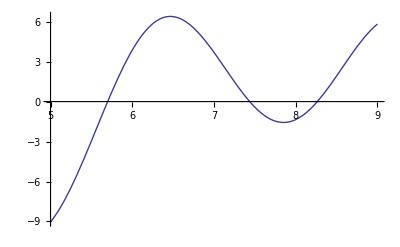

```mathematica
Plot[f[x],{x,5,9}]
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

```mathematica
FindMinimum[f[x],{x,6.5}]
```

{-1.56482,{x→7.85072}}

```mathematica
FindMinimum[{f[x],5≤x≤9},{x,6.5}]
```

{-1.56482,{x→7.85072}}

Then check end points.

```mathematica
f[5]
```

6 Cos[10]+(25 Sin[5])/6

```mathematica
N[6 Cos[10]+(25 Sin[5])/6]
```

-9.02995

```mathematica
f[9]
```

6 Cos[18]+(9 Sin[9])/2

```mathematica
N[6 Cos[18]+(9 Sin[9])/2]
```

5.81643

Therefore, there areMinimums of f(x) on the interval [5,9], which are -1.56482 and it is attained at x=7.85072, and -9.02995 which is attained at x=5

```mathematica
FindMaximum[{f[x],5≤x≤9},{x,7.75}]
```

{6.39064,{x→6.46531}}

Check end points.

```mathematica
f[5]
```

6 Cos[10]+(25 Sin[5])/6

```mathematica
N[6 Cos[10]+(25 Sin[5])/6]
```

-9.02995

```mathematica
f[9]
```

6 Cos[18]+(9 Sin[9])/2

```mathematica
N[6 Cos[18]+(9 Sin[9])/2]
```

5.81643

Therefore, there are two Maximums. One attained at x=6.46531 which equals 6.39064 and one attained at x=9 which equals 5.81643

2) Now use the algebriac tools to determine, with greater accuracy, the absolute and local extreme values of f(x) on the given interval. Prove with second derivative test.

```mathematica
f[x]
```

6 Cos[2 x]+(5 x Sin[x])/(1+x)

```mathematica
f'[x]
```

(5 x Cos[x])/(1+x)-(5 x Sin[x])/(1+x)^2+(5 Sin[x])/(1+x)-12 Sin[2 x]

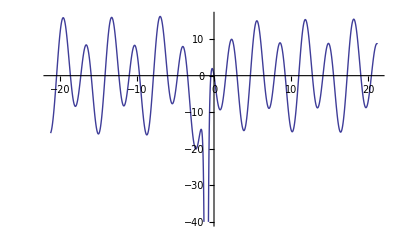

```mathematica
Plot[(5 x Cos[x])/(1+x)-(5 x Sin[x])/(1+x)^2+(5 Sin[x])/(1+x)-12 Sin[2 x],{x,-21.205750411731103,21.205750411731103}]
```

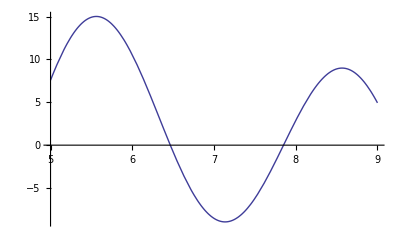

```mathematica
Plot[f'[x],{x,5,9}]
```

```mathematica
FindRoot[f'[x]==0,x]
```

FindRoot::fdss: Search specification x should be a list with 1 to 5 elements.

```mathematica
FindRoot[f'[x]==0,x]
```

```mathematica
?FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

```mathematica
critnos=x/.FindRoot[f'[x],{x,6.5,7.9}]
```

7.85072

```mathematica
FindRoot[f'[x],{x,6.5}]
```

{x→6.46531}

```mathematica
FindRoot[f'[x],{x,7.8}]
```

{x→7.85072}

```mathematica
critnum1=x/.FindRoot[f'[x],{x,6.5}]
```

6.46531

```mathematica
f'[critnum1]
```

6.21725×10^-15

```mathematica
f''[critnum1]
```

-23.0376

Therefore, the extreme max is  6.39064 and it is attained at x=6.46531.
The local max is 5.81643 and it is attianed at x=9.

```mathematica
critnum2=x/.FindRoot[f'[x],{x,7.8}]
```

7.85072

```mathematica
f'[critnum2]
```

-7.32747×10^-15

```mathematica
f''[critnum2]
```

19.5504

Therefore, local min is -1.56482 and it is attained at x=7.85072.
The extreme min is  -9.02995 and it is attained at x=5.

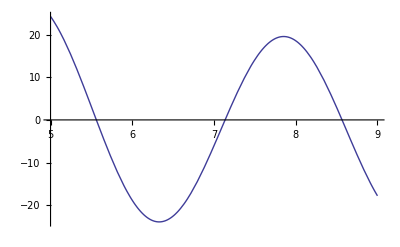

```mathematica
Plot[f''[x],{x,5,9}]
```

```mathematica
Quit[]
```